```mathematica
f[m_,s_,c_,r_]:=1/2 (√(1/s^2) s+Erf[(c+m-r)/(√2 s)]+(Erf[m/(√2 s)]-Erf[(c+m-r)/(√2 s)]) HeavisideTheta[c-r])
```

```mathematica
g[phi_,m_,s_,c_,r_]:=HeavisideTheta[c-r]+phi*(c/r)*f[m,s,c,r]*HeavisideTheta[r-c]
```

1

2

1/2

1/2 (1-Erf[√2])

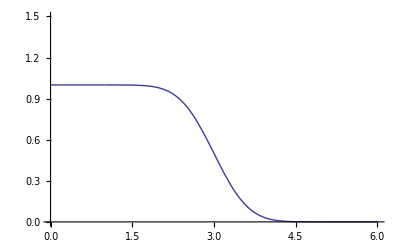

```mathematica
fphi[r_,c_] := 1+HeavisideTheta[r-c]*(r-c)
c = 1
m = 2*c
s = m/4
g[fphi[4,c],m,s,c,4]
Plot[g[fphi[r,c],m,s,c,r],{r,0,6},PlotRange->{Automatic,{0,1.5}}]
```